Membrane Interaction Forces

v1.2
2020-01-15
Based on “Membrane approach 1.nb” v2.1

Modeling the membrane-membrane interactions at the 1-40 nm range that membranes start from then must converge to during fusion
Looking at this via pressure, P

Pro-tip: Mathematica notation for scientific notation is 3.14*^-15

## First pass: Interactions between tensionless, uncharged membranes

Since they're uncharged, we can neglect the electrostatics
Keeping them tensionless here lets us ignore the poorly characterized (ie no one has an equation for it) suppression of undulations by tension

Thus P_tot = P_hydration + P_undulation + P_vdw

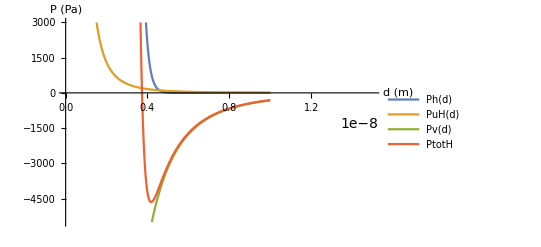

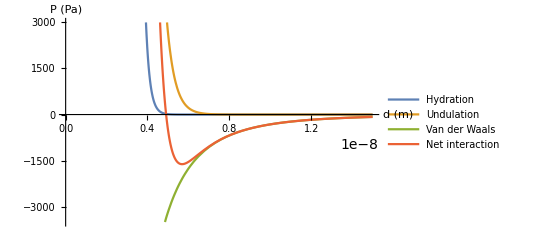

```mathematica
kT = 4.28*^-21; (*in J @ 37C*)
P0 = 1*^12; (*in Pa, hydration P at zero separation*)
c = 0.2*^-9; (*in m, hydration decay const*)
a = 0.2*^-9; (*in m, undulatory decay const*)
B = 10*kT; (*in J, Helfrich bending const*)
H = 1*kT; (*in J, Haymaker const*)
t = 5*^-9; (*in m, thickness of lipid bilayer*)

Ph[d_]:=P0 * Exp[-d/c] (*Hydration repulsion*)
PuH[d_]:=(3*(kT^2))/(4*(Pi^3)*B*(d^3)) (*Helfrich undulation pressure*)
PuR[d_]:=((Pi*kT)/(32*a))*Sqrt[P0/(B*a)]*Exp[-d/(2*a)] (*Rand undulation pressure*)
Pv[d_]:=(-H/(6*Pi))*((1/d^3)-(2/(d+t)^3)+(1/d+2*t)^3) (*van der Waals attraction*)

PtotH=Ph[d]+PuH[d]+Pv[d];
PtotR = Ph[d]+PuR[d]+Pv[d];
Plot[{Ph[d],PuH[d],Pv[d],PtotH},{d,1*^-9,10*^-9},PlotRange->{{0,15*^-9},{-5500,3000}},PlotLegends->"Expressions",AxesLabel->{"d (m)","P (Pa)"}]
Plot[{Ph[d],PuR[d],Pv[d],PtotR},{d,2*^-9,15*^-9},PlotRange->{{0,15*^-9},{-3500,3000}},PlotLegends->{"Hydration", "Undulation","Van der Waals","Net interaction"},AxesLabel->{"d (m)","P (Pa)"}]
```

Great! We see a single clear point of equilibrium.  Note that P_vdw has been graphed as an absolute value.

It’s hard to tell what how Ph and Pu compare to each other (ie which is the greater contributor) from these plots, so let’s plot them alone

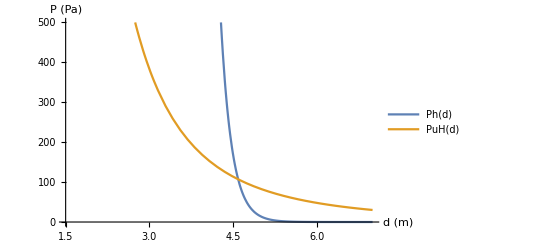

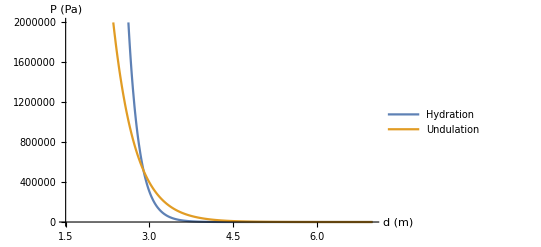

```mathematica
Plot[{Ph[d],PuH[d]},{d,0.5*^-9,7*^-9},PlotRange->{{1.5*^-9,7*^-9},{0,500}},PlotLegends->"Expressions",AxesLabel->{"d (m)","P (Pa)"}]
Plot[{Ph[d],PuR[d]},{d,1.5*^-9,7*^-9},PlotRange->{{1.5*^-9,7*^-9},{0,2*^6}},PlotLegends->{"Hydration","Undulation"},AxesLabel->{"d (m)","P (Pa)"}]
```

So...
	Ph > PuH for d < ~4.6E-9 m
	Ph > PuR for d < ~2.8E-9 m

OK, let’s get a feel for what this all looks like at short range

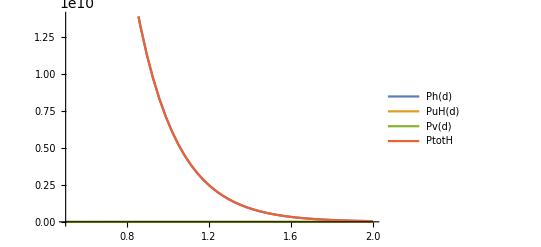

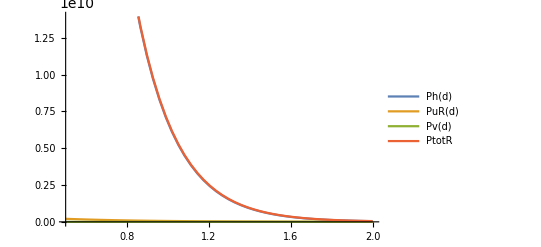

```mathematica
Plot[{Ph[d],PuH[d],Pv[d],PtotH},{d,0.5*^-9,2*^-9},PlotLegends->"Expressions"]
Plot[{Ph[d],PuR[d],Pv[d],PtotR},{d,0.5*^-9,2*^-9},PlotLegends->"Expressions"]
```

Now let's plot everything I might use in my lit review and convert things to nm

```mathematica
PhNm[d_]:=P0 * Exp[-(d*1*^-9)/c] 
PuRNm[d_]:=((Pi*kT)/(32*a))*Sqrt[P0/(B*a)]*Exp[-(d*1*^-9)/(2*a)] 
PvNm[d_]:=(-H/(6*Pi))*((1/(d*1*^-9)^3)-(2/((d*1*^-9)+t)^3)+(1/(d*1*^-9)+2*t)^3) 

Plot[{PhNm[d],PuRNm[d],PvNm[d]},{d,2,15},PlotRange->{{0,15},{-3500,3000}},PlotLegends->{"Hydration", "Undulation","Van der Waals","Net interaction"},AxesLabel->{"d (nm)","P (Pa)"}]
```

SetDelayed::write: Tag Times in (1000000000000000000000 ⅇ^(-5.×10^9 d))[d_] is Protected.

$Failed

SetDelayed::write: Tag Times in (7.18087×10^17 ⅇ^(-2.5×10^9 d))[d_] is Protected.

$Failed

SetDelayed::write: Tag Times in (-2.27061×10^-13 ((1/100000000+1/d)^3+1/d^3-2/(1/200000000+d)^3))[d_] is Protected.

$Failed

General::munfl: Exp[-1.00013×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.13279×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.26544×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

## Second Pass: Interactions between generic biological membranes

This adds electrostatics to the mix and uses the constant values defined in Paper 1 v1

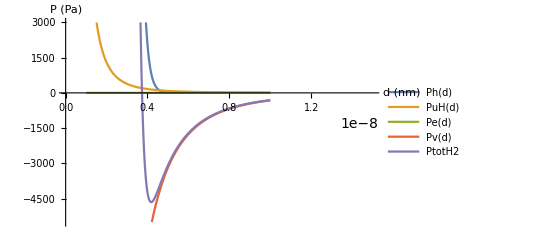

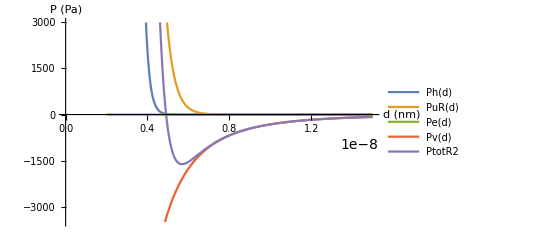

```mathematica
r = -0.015; (*in C/m^2, membrane surface charge density*)
dielec = 60;  (*dimensionless, dielectric constant*)
debye = 0.8*^-9; (* in m, Debye constant of the solution*)

Pe[d_] := (r^2)/(2*dielec*(Sinh[d/(2*debye)])^2) (* electrostatic interaction *)

PtotH2 = PtotH + Pe[d];
PtotR2 = PtotR + Pe[d];
Plot[{Ph[d],PuH[d],Pe[d],Pv[d],PtotH2},{d,1*^-9,10*^-9},PlotRange->{{0,15*^-9},{-5500,3000}},PlotLegends->"Expressions",AxesLabel->{"d (nm)","P (Pa)"}]
Plot[{Ph[d],PuR[d],Pe[d],Pv[d],PtotR2},{d,2*^-9,15*^-9},PlotRange->{{0,15*^-9},{-3500,3000}},PlotLegends->"Expressions",AxesLabel->{"d (nm)","P (Pa)"}]
```

These are practically identical to pass 1!  Pe appears to be totally negligible.  Let’s check to make sure that it’s actually being evaluated at all since you can barely even see it on the graphs:

```mathematica
PuR[5*^-9]
Pe[5*^-9]
```

2676.06

1.45345×10^-8

Yep, it' s being evaluated.  Pe really is just tiny!